TTTR simulation

Introduction  paclet:Fretica/tutorial/TTTRSimulation#178225958 | Simulation of internal-state dynamics  paclet:Fretica/tutorial/TTTRSimulation#720023137
Simulation of particle trajectories of a mixture of species  paclet:Fretica/tutorial/TTTRSimulation#449251965 | Simulation of the photons  paclet:Fretica/tutorial/TTTRSimulation#342625089

```mathematica
Needs["Fretica`"]
```

Introduction

Fretica can be used to simulate realistic TTTR data as they are typically measured in free diffusion experiments. The simulation contains three steps. First the diffusive motion of a mixtures of particles through free space is simulated. The mixture can contain species with different diffusion coefficients. The center of the confocal volume is supposed to be located at the origin of the space coordinates. In the second step one can simulate for each particle internal state dynamics according to kinetic scheme described by rate matrices K for each species. K can contain particle position dependent rate coefficients, e.g. for simulating fluorophore bleaching. In the final step one defines for each species and each internal state mean photon rates for the detection channels. The photon rates are given for the particles is located at the center of the confocal volume. In Addition one can define background rates for all detection channel. Based on these setting Fretica simulates photon time series (TTTR data) for the particles diffusing through the confocal volume. It is also possible to simulate the micro-times of the TTTR records. For this one needs to define for each internal state micro-time distributions. This is also possible for the background signals.

Simulation of particle trajectories of a mixture of species

With FTSSetNumberOfSpecies[N_s] one sets the number N_s of species to be simulated. Different species can have different diffusion coefficients. The species are labelled with integers running from 1 to N_s.

```mathematica
?FTSSetNumberOfSpecies
```

FTSSetNumberOfSpecies[SubscriptBox[
StyleBox[ sets the number N_s of species to be simulated. 
FTSGetNumberOfSpecies[] returns the value set by FTSSetNumberOfSpecies.

```mathematica
?FTSGetNumberOfSpecies
```

FTSGetNumberOfSpecies[] returns the value set by FTSSetNumberOfSpecies.

Different commands can be used to simulate for each species particle trajectories:

FTSSimulateParticleDiffusion

FTSSimulateParticleDiffusionInClosedSphere

FTSSimulateParticleDiffusionInClosedCylinder

FTSSimulateImmobilizedParticle

### FTSSimulateParticleDiffusion

This command is used to simulate particle diffusion inside an open sphere of radius R. For saving computation time and computer memory either a radial symmetric or a cylindrical symmetric confocal volume located at the center of the simulation sphere is assumed. In the case of radial symmetry, the problem reduces to one dimension, only the fluctuation of the radial distance r from the origin needs to be simulated. This is done using the one dimensional equation of motion for Brownian dynamics:

r(t+1)==r(t)+(2DΔt)/(r(t))+Δr

Here r(t) is the radial distance at simulation step t==1..T, where T is the length of the simulation in units of Δt, the time between two simulation steps, D is the diffusion coefficient of the particle, and Δr is a random distance drawn from a normal distribution with mean of zero and a variance of σ^2==2DΔt. In the case of cylindrical symmetry the problem is two dimensional and fluctuations of the distance to the z-axis ρ(t) and of the the z-coordinate z(t) are simulated according to:

ρ(t+1)==ρ(t)+DΔt/(ρ(t))+Δρ

and

z (t + 1) == z (t) + Δ z

Δρ and Δz are a random distances drawn from the normal distribution with mean of zero and a variance of σ^2==2DΔt. The simulation is initialized by randomly distributing particles of the species simulated into the simulation sphere. The number of initial particles is drawn from a Poisson distribution with mean n_0==4/3 π R^3 c_0, where c_0 is the number concentration of the simulated species. Each particle is simulated until it leaves the sphere. In order to keep the mean concentration of particles constant near the center of the sphere, the loss at the sphere’s surface is compensated by periodically (periodicity T_new) placing new particles randomly inside close to the boundary. The distribution of new particles c_new(r) that entered the sphere after a time T_new is obtained by solving the radial diffusion equation

(∂c)/(∂t)==D((∂^2 c)/(∂r^2)+2/r(∂c)/(∂r))

with the initial distribution c(r<R,t==0)==0 and the boundary conditions: c(r==R,t)==c_0 and c(r→0,t)==0. The solution, which describes how an initially empty sphere is filling over time, is given by Crank1975

(c(r,t))/c_0==1+(2R)/πr∑_(n==1)^∞ (-1)^n/n sin(nπr/R)exp(-D n^2 π^2 t/R^2)

c_new(r) is then given by c_new(r)==c(r,T_new). The mean number of particles entering the sphere is calculated by integration over the volume of the sphere

n_new/n_0==1+6/π^2∑_(n==1)^∞ 1/n^2 exp(-D n^2 π^2 T_new/R^2)

After each time interval T_new a random number of new particles is drawn from the Poisson distribution with mean n_new. They are placed at radial distances randomly chosen from the distribution with the density function P_new(r)==c_new(r)4π r^2/n_new for r<R. In two dimensions initial coordinates are obtained as z==rcos(θ) and ρ==√(r^2-z^2) , where cos(θ) is randomly chosen between -1 and 1. The Brownian motion of each new particle is again simulated until it leaves the sphere.

```mathematica
?FTSSimulateParticleDiffusion
```

FTSSimulateParticleDiffusion[SubscriptBox[
StyleBox[ simulates Brownian motion of particles in an open sphere. Particles are simulated until they leave the sphere. Periodically, new particles appear at the inner boundary of the sphere to maintain a constant concentration within the sphere.  
i_s:   The species index i_s defines the species that will be simulated. i_s can run from 1 ...  
StyleBox[, if FTSSetNumberOfSpecies[N] was executed before. 
R:   Radius of the simulation sphere in micrometers. 
D:   Diffusion coefficient in μ SuperscriptBox[m, 2]/μ  s. 
c_0:   Number concentration of particles in 1/μ SuperscriptBox[m, 3]. 
T:   Total length of the simulation in units of Δ. T is an integer and defines the total number of simulations steps. 
Δ:   Simulation step size in microseconds. 
T_new:   Period of time steps after which new particles appear randomly inside the sphere. T_new in units of Δ is an integer. 
T_min:   Only particle trajectories longer than T_min are saved to memory. T_min in units of Δ is an integer. 
R_save:   Only those particle trajectories are saved to memory that go below R_save for at least one simulation step. Of those trajectories, only the segments for which r and the durations of the gaps between such segments are saved. 
FTSSimulateParticleDiffusion has the options Method→"1D" (default) or Method→"2D". Correspondingly only the radial distances to the origin ("1D") or the distances to the z-axis and the z coordinates ("2D") are simulated and saved to memory.

### FTSSimulateParticleDiffusionInClosedSphere

FTSSimulateParticleDiffusionInClosedSphere is used to simulate particle diffusion inside a closed sphere. Particles are either reflected of adsorbed at the boundary. No new particles are entering the sphere. As in FTSSimulateParticleDiffusion only the radial distance fluctuations r(t) are simulated.

```mathematica
?FTSSimulateParticleDiffusionInClosedSphere
```

FTSSimulateParticleDiffusionInClosedSphere[SubscriptBox[
StyleBox[ R_save p_absorb simulates Brownian motion of particles in a closed sphere.  
i_s:   The species index i_s defines the species that will be simulated. i_s can run from 1 ...  SubscriptBox[
StyleBox[, if FTSSetNumberOfSpecies[N] was executed before. 
R:   Radius of the simulation sphere in micrometers. 
D:   Diffusion coefficient in μ SuperscriptBox[m, 2]/μ  s 
n_0:   Initial number of particles in the sphere. 
T:   Total length of the simulation in units of Δ. T is an integer and defines the total number of simulations steps. 
Δ:   Simulation step size in microseconds. 
R_save:   Only parts with r and the lengths of the gaps between such parts are saved. 
p_stick The probability (0 ...  1) that a particle that hits the boundary is absorbed. If it is not absorbed, it is reflected.

### FTSSimulateParticleDiffusionInClosedCylinder

FTSSimulateParticleDiffusionInClosedCylinder is used to simulate particle diffusion inside a closed cylinder. Particles are either reflected of adsorbed at the boundary. No new particles are entering the cylinder. Particle positions are stored in cylinder coordinates. Radial symmetry around the z-axis is assumed. Only the fluctuations of the distance to the z-axis ρ(t) and of the the z-coordinate z(t) are simulated according to:

ρ(t+1)==ρ(t)+DΔt/(ρ(t))+Δρ

and

z (t + 1) = z (t) + Δ z

Here ρ(t) is the distance from the z-axis at simulation step t==1..T, where T is the length of the simulation in units of Δt, the time between two simulation steps. z(t) is the z-coordinate at time step t. D is the diffusion coefficient of the particle. Δρ and Δz are a random distances drawn from the normal distribution with mean of zero and a variance of σ^2==2DΔt.

```mathematica
?FTSSimulateParticleDiffusionInClosedCylinder
```

FTSSimulateParticleDiffusionInClosedCylinder[SubscriptBox[
StyleBox[ Δ simulates Brownian motion of particles in a closed cylinder.  
i_s:   The species index i_s defines the species that will be simulated. i_s can run from 1 ...  SubscriptBox[
StyleBox[, if FTSSetNumberOfSpecies[N] was executed before. 
R:   Radius of the simulation cylinder in micrometers. 
l_(1/2):   Half-length of the simulation cylinder in micrometers. 
D:   Diffusion coefficient in μ SuperscriptBox[m, 2]/μ  s 
n_0:   Initial number of particles in the cylinder. 
T:   Total length of the simulation in units of Δ. T is an integer and defines the total number of simulations steps. 
Δ:   Simulation step size in microseconds. 
R_save:   Only segments with r and the durations of the gaps between such segments are saved. 
p_stick:   The probability (0 ...  1) that a particle that hits the boundary is absorbed. If it is not absorbed, it is reflected.

### FTSSimulateImmobilizedParticle

```mathematica
?FTSSimulateImmobilizedParticle
```

FTSSimulateImmobilizedParticle[
StyleBox[ generates a trajectory of a particle that is immobilized at the origin, i.e., at the center of the confocal volume.  
T:   Total length of the simulation in units of Δ. T is an integer and defines the total number of simulations steps. 
Δ:   Simulation step size in microseconds.

### Special commands

```mathematica
?FTSGetTrajectories
```

FTSGetTrajectories[SubscriptBox[
StyleBox[ returns a list of simulated trajectories of species i_s  
i_s:   species index 
FormBox[
StyleBox["k", "TI"]; ; 
StyleBox["l", "TI"],
TraditionalForm]:   Trajectories k to l are returned. With FormBox[1; ; 
StyleBox["A", "TI"] 
StyleBox["l", "TI"] 
StyleBox["l", "TI"],
TraditionalForm], all trajectories are returned. 
Δ:   For each trajectory, only every Δ  th particle position is returned. 
r_max:   Only positions with r are returned. With r_max, all positions are returned. 
The output of FTSGetTrajectories is of the form htt. It can be passed on to FTSDistanceTrajectory or FTSIntensityTrajectory

```mathematica
?FTSDistanceTrajectory
```

FTSDistanceTrajectory[ trlist ] transforms particle coordinates contained in trlist to distances to the center of origin. trlist can be any output of FTSGetTrajectories.

```mathematica
?FTSIntensityTrajectory
```

FTSIntensityTrajectory[trlist,I_0 returns a list of trajectories with pairs of time and intensity assuming a Gaussian-shaped confocal volume centered at the origin.  
trlist:   This can be any output of FTSGetTrajectories. 
I_0:   Intensity detected from a particle located at the origin. 
w_0:   Lateral dimension (semi-minor axis) of the confocal volume in micrometers. 
z_0:   Axial dimension (semi-major axis) of the confocal volume in micrometers. 
Depending on the data format in trlist, the intensity as a function of particle position is calculated in cylindrical coordinates according to I or in spherical coordinates according to I.

Simulation of internal-state dynamics

After particle trajectories were simulated for all species with the commands described above, one can add internal-state dynamics to the particles. For a system with N_st internal states we define a quadratic N_st×N_st rate matrix K such that the kinetics is described by the rate equation

d/dt p==Kp,

where the vector p describes the population of states 1... N_st. The rate matrix is in the most general case of the form K==K_0+I(r)K_1. The second term which is proportional to the intensity distribution of the excitation volume I(r) allows to model photo-physical effects like blinking and bleaching. For each particle of a species i_s with position trajectory r_t and starting time t_0 a state trajectory s_t is simulated by calling the function FTSSimulateStateTrajectories. The initial state s(t_0) is randomly chosen according to the initial probabilities for the states 1... N_st. Theses values are listed in a vector named p_0. For all later times t the state s(t) is simulated based on the state before, s(t-1), by randomly choosing from the probability distribution formed by column s(t-1) of the transition matrix A==exp(KΔt) .

Together with the state kinetics also the observation matrix B is defined by calling FTSSimulateStateTrajectories. B is a N_st×N_d matrix, where the matrix element b_sd defines the mean photon detection rate on detector d of a particle in state s that is located at the origin, i.e. at the center of the confocal volume. The index d is running from one to the total number of detection routes N_d.

```mathematica
?FTSSimulateStateTrajectories
```

FTSSimulateStateTrajectories[{SubscriptBox[
StyleBox[ or 
FTSSimulateStateTrajectories[{SubscriptBox[
StyleBox[ defines mean photon detection rates of internal states and simulates internal-state dynamics for all particles of species i_s. The kinetics are given by the rate equation d/dt, where the (N_st) rate matrix K is given by K or K. The vector p describes the population of states 1 ...  SubscriptBox[
StyleBox[ as a function of time.  
i_s:   species index 
B:   This N_st matrix defines the mean photon detection rates for a particle that is located at the origin. N_st is the number of states and N_D the number of detection routes. The matrix element b_sd defines the mean photon detection rate on detector d of a particle in state s. 
p_0:   vector of length N_st containing the initial relative probabilities of a particle to be in state 1 ...  SubscriptBox[
StyleBox[ at the start of the trajectory. 
K_0:   The part of the rate matrix that is independent of the particle position. 
K_1:   The second version of the command allows position-dependent processes such as photobleaching to be modeled. The total rate matrix is then given by K, where I is the excitation intensity distribution of the confocal volume. Depending on the format of the trajectories, I is calculated in cylindrical coordinates according to I or in spherical coordinates according to I. 
w_0:   Lateral dimension (semi-minor axis) of the confocal volume in micrometers. 
z_0:   Axial dimension (semi-major axis) of the confocal volume in micrometers. 
r_max:   For distances to the origin with |
StyleBox[, the excitation intensity is set to zero, I. 
FTSSimulateStateTrajectories[{SubscriptBox[
StyleBox[ is equivalent to calling FTSSimulateStateTrajectories[{SubscriptBox[
StyleBox[ with K_0 set to the zero matrix of suitable dimension. Calling FTSSimulateStateTrajectories[{SubscriptBox[
StyleBox[ is equivalent to FTSSimulateStateTrajectories[{SubscriptBox[
StyleBox[ .

Alterantively to FTSSimulateStateTrajectories one can use FTSSimulateFRETStateTrajectories to simulate two-channel FRET data, where for each state and for each trajectory the mean transfer efficiency is randomly chosen from beta distributions. With this inhomogeneous broadening can be mimiced.

```mathematica
?FTSSimulateFRETStateTrajectories
```

FTSSimulateFRETStateTrajectories[{SubscriptBox[
StyleBox[ or 
FTSSimulateFRETStateTrajectories[{SubscriptBox[
StyleBox[, FormBox[
StyleBox["rcm", "TB"], α}, SubscriptBox[
StyleBox["w", "TI"], "0"], SubscriptBox[
StyleBox["z", "TI"], "0"], SubscriptBox[
StyleBox["r", "TI"], "max"]],
TraditionalForm] 
defines photon statistics of internal states and simulates internal-state dynamics for all particles of species i_s. The kinetics are given by the rate equation d/dt, where the (N_st) rate matrix K is given by K or K. The vector p describes the population of states 1 ...  SubscriptBox[
StyleBox[ as a function of time.  
i_s:   species index 
fretmodel:   is of the form FormBox[{{SubscriptBox[
StyleBox["n", "TI"], "1"], SubscriptBox[
StyleBox["e", "TI"], "1"], SubscriptBox[ν, 1]},  ... , {SubscriptBox[
StyleBox["n", "TI"], SubscriptBox[
StyleBox["N", "TI"], 
StyleBox[
RowBox[{"s", "t"}], "TI"]]], SubscriptBox[
StyleBox["e", "TI"], SubscriptBox[
StyleBox["N", "TI"], 
StyleBox[
RowBox[{"s", "t"}], "TI"]]], SubscriptBox["ν", SubscriptBox[
StyleBox["N", "TI"], 
StyleBox[
RowBox[{"s", "t"}], "TI"]]]}},
TraditionalForm]. 
p_0:   vector of length N_st containing the initial relative probabilities of a particle to be in state 1 ...  SubscriptBox[
StyleBox[ at the start of the trajectory. 
K_0:   The part of the rate matrix that is independent of the particle position. 
K_1:   The second version of the command allows position-dependent processes such as photobleaching to be modeled. The total rate matrix is then given by K, where I is the excitation intensity distribution of the confocal volume. Depending on the format of the trajectories, I is calculated in cylindrical coordinates according to I or in spherical coordinates according to I. 
rcm:   2×2 RCM. 
w_0:   Lateral dimension (semi-minor axis) of the confocal volume in micrometers. 
z_0:   Axial dimension (semi-major axis) of the confocal volume in micrometers. 
r_max:   For distances to the origin with |
StyleBox[, the excitation intensity is set to zero, I. 
For each simulated particle trajectory j the transfer efficiencies E_(j,1) of the internal states s are randomly chosen from the beta distributions BetaDistribution [SubscriptBox[
StyleBox[. The photon detection rates on detector 1 (acceptor channel) and detector 2 (donor channel) for photons coming from particle j while being in internal state s are then given by Inverse[rcm] . (
StyleBox[. 
FTSSimulateFRETStateTrajectories[{SubscriptBox[
StyleBox[ is equivalent to calling FTSSimulateStateTrajectories[{SubscriptBox[
StyleBox[ with K_0 set to the zero matrix of suitable dimension. Calling FTSSimulateFRETStateTrajectories[{SubscriptBox[
StyleBox[ is equivalent to FTSSimulateStateTrajectories[{SubscriptBox[
StyleBox[ .

Simulation of the photons

In the final step photons and corresponding TTTR records are simulated. For a given time t the mean detection rate on detector d is given by a sum over fluorescence rates of all particles of all species plus a background rate:

n_d(t)==∑_(i_s==0)^N_s ∑_(p==0)^(N_p(i_s,t)) I(r_(i_s,p)(t)) b_i_s(s_(i_s,p)(t),d)+n_bg(d)

Here N_p(i_s,t) is the number of particles of species i_s present in the simulation volume at time t. r_(i_s,p)(t) and s_(i_s,p)(t) are the position and state trajectories of the pth particle of species i_s. b_i_s(s,d) is the mean detection rate on detector d of a particle of species i_s in state s that is located at the origin. For each time step t==1...T a time δt is randomly drawn from the exponential distribution with density function n_tot(t)exp(-n_tot(t)δt), where n_tot(t)==∑_(d==1)^N_d n_d(t) is the total mean photon rate at time t. If δt is smaller than the duration of a time simulation step, i.e. if δt<Δt, then we add a photon, detected at time tΔt+δt, to the list of TTTR records. The detection route of the photon is randomly chosen according the relative magnitudes of detection rates n_d(t) with d==1... N_d.

```mathematica
?FTSSimulateTTTR
```

FTSSimulateTTTR[{SubscriptBox[
StyleBox[ simulates photons (TTTR records) using the beforehand simulated particle trajectories and state trajectories, as well as the photon detection rates of the states. Depending on the nature of trajectories the excitation light intensity distribution I of the confocal valumes is given in cylinder coordinates according to I or in in polar coordinates according to I.  
FormBox[{SubscriptBox[
StyleBox["n", "TI"], 
RowBox[{
StyleBox["b", "TI"], 
StyleBox["g", "TI"], ",", "1"}]],  ... , SubscriptBox[
StyleBox["n", "TI"], 
RowBox[{
StyleBox["b", "TI"], 
StyleBox["g", "TI"], ",", SubscriptBox[
StyleBox["N", "TI"], 
StyleBox["d", "TI"]]}]]},
TraditionalForm]:   List of mean background rates of the detection channels. 
r_max:   For distances to the origin larger than |
StyleBox[ the excitation intensity is set to zero I. 
w_0:   Lateral dimension of confocal volume in μm. 
z_0:   Axial dimension of confocal volume in μm. 
Only macro-times are simulated. Micro-times, i.e. lifetime-channels, can be simulated for the photons using FTSSimulateTTTRLifeTimes.

With the command FTSSimulateTTTRLifeTimes one can add to each photon that was simulated with FTSSimulateTTTR a simulated lifetime-channel. For this one needs to specify for all internal states of all species corresponding lifetime-channel distributions for all detection routes. Also for the background photons lifetime-channel distributions can be attributed to all detection routes.

```mathematica
?FTSSimulateTTTRLifeTimes
```

FTSSimulateTTTRLifeTimes[nbg,SubscriptBox[
StyleBox[ chdis, bgdis] simulates microtimes (lifetime channels) for the photons simulated beforehand with FTSSimulateTTTR.  
nbg:   List of mean background rates of the detection channels: FormBox[{SubscriptBox[
StyleBox["n", "TI"], 
RowBox[{
StyleBox["b", "TI"], 
StyleBox["g", "TI"], ",", "1"}]],  ... , SubscriptBox[
StyleBox["n", "TI"], 
RowBox[{
StyleBox["b", "TI"], 
StyleBox["g", "TI"], ",", SubscriptBox[
StyleBox["N", "TI"], 
StyleBox["d", "TI"]]}]]},
TraditionalForm] 
r_max:   For distances to the origin larger than |
StyleBox[ the excitation intensity is set to zero I. 
w_0:   Lateral dimension of confocal volume in μm. 
z_0:   Axial dimension of confocal volume in μm. 
chdis:   Nested list where chdis[[SubscriptBox[
StyleBox[ is a list of numbers representing the lifetime-channel distribution on detector d of fluorescence photons from a particle of species i_s being in state i_st. 
bgdis:   List of length N_d where bgdis[[
StyleBox[ is a list of numbers representing the lifetime-channel distribution of background photons on detector d.

Introduction  paclet:Fretica/tutorial/TTTRSimulation#178225958 | Simulation of internal-state dynamics  paclet:Fretica/tutorial/TTTRSimulation#720023137
Simulation of particle trajectories of a mixture of species  paclet:Fretica/tutorial/TTTRSimulation#449251965 | Simulation of the photons  paclet:Fretica/tutorial/TTTRSimulation#342625089

Examples

```mathematica
Needs["Fretica`"]
```

Build time: Aug 27 2020  13:41:32

### Example 1: Mixture of species with D_1=5 D_2, no internal states, labeled with different dyes

#### Parameters

```mathematica
FTSSetNumberOfSpecies[2];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.5;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;


diff1=0.0001;(* μm^2/μs *)
c1=30. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)

diff2=0.00002;(* μm^2/μs *)
c2=30. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.4;z0=1.; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
```

0.890932

#### T_new cycle

```mathematica
4/3 π Rsphere^3 c1
FTSMeanNewParticleNumberInSphere[Rsphere,diff1,c1,Tnew]
```

2.04322

0.660963

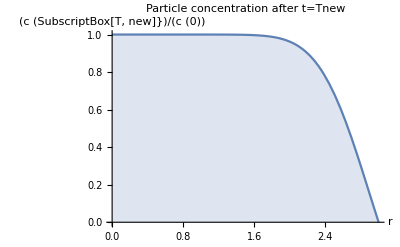

```mathematica
Plot[1-FTSNewParticleConcentration[Rsphere,diff1,c1,r,dt*Tnew]/c1,{r,0,Rsphere},Frame->False,Filling->Bottom,PlotLabel->"Particle concentration after t=Tnew",PlotRange->All,AxesLabel->{"r","(c (SubscriptBox[T, new]})/(c (0))"}]
```

#### Simulation of r-trajectories

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"2D"]//AbsoluteTiming
```

{112.755,41890}

```mathematica
FTSSimulateParticleDiffusion[2,Rsphere,diff2,c2,T,dt,Tnew,Tmin,Rsave,Method->"2D"]//AbsoluteTiming
```

{152.678,8299}

```mathematica
sim=FTSGetTrajectories[1,1;;25,3.,10];
ListPlot[Select[FTSDistanceTrajectory[sim],UnsameQ[#,{}]&],PlotLabel->"Species 1",AxesLabel->{"time(sec)", "r (μm)"}]
```

-Graphics-

```mathematica
sim=FTSGetTrajectories[2,1;;3,3.,10];
ListPlot[Select[FTSDistanceTrajectory[sim],UnsameQ[#,{}]&],PlotLabel->"Species 2",AxesLabel->{"time(sec)", "r (μm)"}]
```

-Graphics-

#### Set photon rates

The photon rate depends on the particle’s position in the confocal volume.
Typically the dependence is described by a 3D Gaussian:

n(r)=n(x,y,z)=n_0 exp((-2(x^2+y^2))/w_0^2)exp((-2 z^2)/z_0^2)

```mathematica
w0=.4;z0=1.; (*μm*)
Veff=π^(3/2)w0^2 z0  (*volume of confocal volume*)
Neff=Veff c1 (* mean particle number in confocal volume*)
```

0.890932

0.0160956

Define photon rates at the center of the confocal volume  for each channel :

```mathematica
n01={1.,0}; (*counts/μs,  species 1*)
n02={0,2.}; (*counts/μs, species 2*)

FTSSimulateStateTrajectories[{1,{n01},{1}}];
FTSSimulateStateTrajectories[{2,{n02},{1}}];
```

#### Simulate photons

```mathematica
rmax=2.; (*up to this distance particle can contribute photons*)
```

```mathematica
Exp[-2 rmax^2/z0^2]
```

0.000335463

```mathematica
bg1=0;  (* background rate on detection channel 1 *)
bg2=0 ; (* background rate on detection channel 2 *)
```

```mathematica
AbsoluteTiming[FTSSimulateTTTR[{bg1,bg2},rmax,w0,z0]]
```

{35.2513,1}

#### Photon Traces (MCS traces)

```mathematica
FMCStrace[{{1,0},{0,1}},1,0,5]
```

-Graphics-

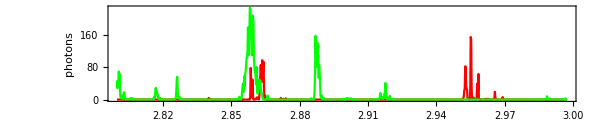

```mathematica
FMCStrace[{{1,0},{0,1}},0.2,2.8,3]
```

#### FCS

{35.1995,1}

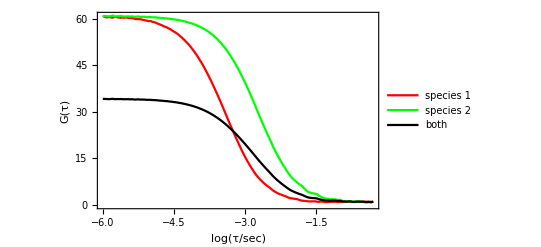

```mathematica
AbsoluteTiming[FTSSimulateTTTR[{0,0},2.0,w0,z0]]
Show[FFCSW[-5.9,0.,{1,0,0,0},{1,0,0,0},FOutput->FGraph,PlotStyle->Red],
FFCSW[-5.9,0.,{0,1,0,0},{0,1,0,0},FOutput->FGraph,PlotStyle->Green],
FFCSW[-5.9,0.,{1,1,0,0},{1,1,0,0},FOutput->FGraph,PlotStyle->Black],Graphics[Inset[LineLegend[{Red,Green,Black},{"species 1","species 2","both"}],Scaled@{.8,.8}]]]
```

```mathematica
1+1/Neff
```

63.1288

#### PCH

```mathematica
FPCH[{{1,0,0,0},{0,1,0,0}},0.2,PlotStyle->{Red,Green}]
```

-Graphics-

### Example 2: FRET-labeled system (static)

#### Simulation r-trajectories

```mathematica
FTSSetNumberOfSpecies[1];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.0;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;
diff1=0.00005;(* μm^2/μs *)
c1=50. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.5;z0=0.5; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
Neff=Veff c1
```

0.696041

0.0209578

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"1D"]//AbsoluteTiming
```

{81.4996,17610}

#### Set photon rates for three states (D, U, N)

correction factors:

```mathematica
γ=1.5; (*correcting for unequal quantum yields and detection efficienies*)
ct=0.08; (*cross talk, i.e. leakage of donor photons into acceptor detection channel*)
α=0.04; (*acceptor direct excitation*)
rcm:=({{1, -ct}, {0, γ}});
```

photon rates:

```mathematica
ntot=0.2 (* photons/μs*) (* at center laser focus*)
eD=0;eU=0.5;eN=0.95; (* transfer efficiencies *)

(*photon rates of ideal instrument and dyes*)
nD=ntot {eD,(1-eD)};
nU=ntot {eU,(1-eU)};
nN=ntot {eN,(1-eN)};

(*photon rates of real instrument and dyes*)
invrcm=Inverse[rcm];
nD=invrcm.nD;
nU=invrcm.((1-α)nU+α ntot{1,0});
nN=invrcm.((1-α)nN+α ntot{1,0});
```

0.2

```mathematica
p0={pD=0.5,pU=1,pN=1}; (* relative populations *)
FTSSimulateStateTrajectories[{1,{nD,nU,nN},p0}]
```

1

#### Simulate photons

```mathematica
rmax=1; (* up to rmax fluorescence rate ist calculated*)
nbgA=  0.0015;
nbgD=   0.003;
AbsoluteTiming[FTSSimulateTTTR[{nbgA,nbgD},rmax,w0,z0]]
```

{13.4441,1}

#### Photon Traces (MCS traces)

```mathematica
FMCStrace[{{1,0},{0,1}},1,0,5]
```

-Graphics-

#### FCS

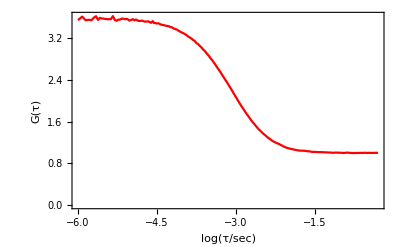

```mathematica
FFCSW[-5.9,0.,{1,1},{1,1},FOutput->FGraph,PlotStyle->Red]
```

```mathematica
1+1/Neff
```

48.7149

#### PCH

```mathematica
FPCH[{{1,0,0,0},{0,1,0,0}},0.2,PlotStyle->{Red,Green}]
```

-Graphics-

#### Burst identification

```mathematica
FSetRCM[rcm];
FSetDirectAcceptorExcitation[α];
```

```mathematica
FDetermineBackground[];
FFindBurstsDeltaT[0.00015,20,10000];
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000]
```

{1675.77,3067.15,0.,0.,0.,0.}

4579

#### Transfer efficiency histogram

```mathematica
fit=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{0,0.5,0.9}];
fit[[2]]
```

-Graphics-

```mathematica
{Pos[1],Pos[2],Pos[3]}/.fit[[1]]
pop=FFRETPeakIntegrate[{"G","G","G"},fit[[1]],{-0.2,1.2}];pop/=Total[pop]
```

{-0.0459678,0.493987,0.938816}

{0.182492,0.409146,0.408363}

### Example 3: FRET-labeled system with state-kinetics

#### Simulation r-trajectories

```mathematica
FTSSetNumberOfSpecies[1];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.0;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;
diff1=0.00005;(* μm^2/μs *)
c1=50. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.5;z0=0.5; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
Neff=Veff c1
```

0.696041

0.0209578

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"1D"]//AbsoluteTiming
```

{81.4996,17610}

#### Set photon rates for three states (D, U, N)

correction factors:

```mathematica
γ=1.5; (*correcting for unequal quantum yields and detection efficienies*)
ct=0.08; (*cross talk, i.e. leakage of donor photons into acceptor detection channel*)
α=0.04; (*acceptor direct excitation*)
rcm:=({{1, -ct}, {0, γ}});
```

photon rates:

```mathematica
ntot=0.2 (* photons/μs*) (* at center laser focus*)
eD=0;eU=0.5;eN=0.95; (* transfer efficiencies *)

(*photon rates of ideal instrument and dyes*)
nD=ntot {eD,(1-eD)};
nU=ntot {eU,(1-eU)};
nN=ntot {eN,(1-eN)};

(*photon rates of real instrument and dyes*)
invrcm=Inverse[rcm];
nD=invrcm.nD;
nU=invrcm.((1-α)nU+α ntot{1,0});
nN=invrcm.((1-α)nN+α ntot{1,0});
```

0.2

#### Simulate state dynamics (U ⇌ N)

```mathematica
kf=0.001;ku=0.001 ; (*1/μs*)
pDonly=0.2;
Km=({{0, 0, 0}, {0, -kf, ku}, {0, kf, -ku}});
p0={pDonly,(1-pDonly)ku/(kf+ku),(1-pDonly)kf/(kf+ku)};
FTSSimulateStateTrajectories[{1,{nD,nU,nN},p0,Km}];
```

#### Simulate photons

```mathematica
rmax=1; (* up to rmax fluorescence rate ist calculated*)
nbgA=  0.0015;
nbgD=   0.003;
AbsoluteTiming[FTSSimulateTTTR[{nbgA,nbgD},rmax,w0,z0]]
```

{13.0931,1}

#### Burst identification

```mathematica
FSetRCM[rcm];
FSetDirectAcceptorExcitation[α];
```

```mathematica
FDetermineBackground[];
FFindBurstsDeltaT[0.00015,20,10000];
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000]
```

{1675.83,3071.7,0.,0.,0.,0.}

4695

#### Transfer efficiency histogram

```mathematica
fit=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{0,0.5,0.9}];
fit[[2]]
```

-Graphics-

### Example 4: FRET-labeled system with photo bleaching

#### Simulation r-trajectories

```mathematica
FTSSetNumberOfSpecies[1];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.0;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;
diff1=0.00005;(* μm^2/μs *)
c1=50. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.5;z0=0.5; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
Neff=Veff c1
```

0.696041

0.0209578

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"1D"]//AbsoluteTiming
```

{81.4996,17610}

#### Set photon rates for four states ( D, U, N, A )

correction factors:

```mathematica
γ=1.5; (*correcting for unequal quantum yields and detection efficienies*)
ct=0.08; (*cross talk, i.e. leakage of donor photons into acceptor detection channel*)
α=0.04; (*acceptor direct excitation*)
rcm:=({{1, -ct}, {0, γ}});
```

photon rates:

```mathematica
ntot=0.2 (* photons/μs*) (* at center laser focus*)
eD=0;eU=0.5;eN=0.95; (* transfer efficiencies *)

(*photon rates of ideal instrument and dyes*)
nD=ntot {eD,(1-eD)};
nU=ntot {eU,(1-eU)};
nN=ntot {eN,(1-eN)};
nA={0,0};

(*photon rates of real instrument and dyes*)
invrcm=Inverse[rcm];
nD=invrcm.nD;
nU=invrcm.((1-α)nU+α ntot{1,0});
nN=invrcm.((1-α)nN+α ntot{1,0});
nA=invrcm.(α ntot{1,0});
```

0.2

#### Simulate state dynamics ( bleaching)

```mathematica
kf=0;ku=0 ; (*1/μs*)
kabl=0.0003;
kdbl=0.00004;
Km=({{0, 0, 0, 0}, {0, -kf, ku, 0}, {0, kf, -ku, 0}, {0, 0, 0, 0}});
Kbleach=({{0, kabl (eU), kabl (eN), 0}, {0, -kabl (eU) -kdbl (1-eU), 0, 0}, {0, 0, -kabl (eN)-kdbl(1-eN), 0}, {0, kdbl (1-eU), kdbl (1-eN), 0}});
p0={0.1,0.4,0.4,0.1};
```

```mathematica
rmax=1; (* up to rmax fluorescence rate ist calculated*)
AbsoluteTiming[FTSSimulateStateTrajectories[{1,{nD,nU,nN,nA},p0,Km,Kbleach},w0,z0,rmax]]
```

{8.47107,1}

#### Simulate photons

```mathematica
nbgA=  0.0015;
nbgD=   0.003;
AbsoluteTiming[FTSSimulateTTTR[{nbgA,nbgD},rmax,w0,z0]]
```

{12.9836,1}

#### Burst identification

```mathematica
FSetRCM[rcm];
FSetDirectAcceptorExcitation[α];
```

```mathematica
FDetermineBackground[];
FFindBurstsDeltaT[0.00015,20,10000];
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000]
```

{1665.13,3058.06,0.,0.,0.,0.}

4090

#### Transfer efficiency histogram

```mathematica
fit=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{0,0.5,0.9}];
fit[[2]]
```

-Graphics-

```mathematica
FCutAsymmetricBursts[2.];
fit=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{0,0.5,0.9}];
fit[[2]]
```

-Graphics-

### Example 5: FRET-labeled system with lifetime-information and PIE

#### Simulation r-trajectories

```mathematica
FTSSetNumberOfSpecies[1];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.0;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;
diff1=0.00005;(* μm^2/μs *)
c1=50. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.5;z0=0.5; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
Neff=Veff c1
```

0.696041

0.0209578

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"1D"]//AbsoluteTiming
```

{100.381,17270}

#### Set photon rates for four states ( D, U, N, A )

correction factors:

```mathematica
γ=1.2; (*correcting for unequal quantum yields and detection efficienies*)
ct=0.08; (*cross talk, i.e. leakage of donor photons into acceptor detection channel*)
α=0.04; (*acceptor direct excitation*)
rcm:=({{1, -ct}, {0, γ}});

pieγ=1.2;
```

photon rates:

```mathematica
ntot=0.2; (* photons/μs at center laser focus*)
eD=0;eU=0.5;eN=0.8; (* transfer efficiencies *)

nDD=ntot {0,1};
nDU=ntot {eU,(1-eU)}+α /(1-α)ntot{1,0};
nDN=ntot    {eN,(1-eN)}+α /(1-α) ntot{1,0};
nDA=α /(1-α) ntot {1,0};

nAD=ntot/pieγ {0,0};
nAU=ntot/pieγ {1,0};
nAN=ntot /pieγ{1,0};
nAA=ntot /pieγ{1,0};
nD=nDD+nAD;
nU=nDU+nAU;
nN=nDN+nAN;
nA=nDA+nAN;

(*photon rates of real instrument and dyes*)
invrcm=Inverse[rcm];
nD=invrcm.nD;nU=invrcm.nU;nN=invrcm.nN;nA=invrcm.nA;
```

#### Simulate state dynamics ( bleaching)

```mathematica
kf=0;ku=0 ; (*1/μs*)
kabl=0.0003;
kdbl=0.00004;
Km=({{0, 0, 0, 0}, {0, -kf, ku, 0}, {0, kf, -ku, 0}, {0, 0, 0, 0}});
Kbleach=({{0, kabl (eU), kabl (eN), 0}, {0, -kabl (eU) -kdbl (1-eU), 0, 0}, {0, 0, -kabl (eN)-kdbl(1-eN), 0}, {0, kdbl (1-eU), kdbl (1-eN), 0}});
p0={0.1,0.4,0.4,0.1};
```

```mathematica
rmax=1; (* up to rmax fluorescence rate ist calculated*)
AbsoluteTiming[FTSSimulateStateTrajectories[{1,{nD,nU,nN,nA},p0,Km,Kbleach},w0,z0,rmax]]
```

{12.6544,1}

#### Simulate photons

```mathematica
nbgA=  0.0015;
nbgD=   0.003;
AbsoluteTiming[FTSSimulateTTTR[{nbgA,nbgD},rmax,w0,z0]]
```

{34.2257,1}

#### IRF

```mathematica
irf=N@FOpenHistoData[$FreticaExamples<>"\\IRF_Fianium_488 nm.hhd"][[1]];
Length[irf]
imax=Length[irf];While[irf[[imax,2]]==0,imax--];
irf=irf[[1;;imax]];
Length[irf]
irfraw=irf;
```

65536

12872

Hydraharp stores 65536 bins, at ~20MHz and 4 ps binning only imax=12872 are used

```mathematica
ListLogPlot[irf,PlotRange->All]
```

-Graphics-

```mathematica
(*Use the irf only up to 4 ns and normalize*)
irf=Select[irf,#[[1]]<4&]; 
irf[[All,2]]/=Total[irf[[All,2]]];
```

```mathematica
ListPlot[irf,PlotRange->All]
ListLogPlot[irf,PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
(*Delete noise*)
maxirf=Max[irf[[All,2]]];
irf[[All,2]]=irf[[All,2]]/.x_?(#<10^-4 maxirf&)->0;
(*Normalize*)
irf[[All,2]]/=Total[irf[[All,2]]];
irf=Total/@Partition[irf,4];
```

```mathematica
ListLogPlot[irf,PlotRange->All]
```

-Graphics-

#### life time simulation (assuming Gaussian-Chain for U and static distance for N)

```mathematica
conv[decay_]:=ListConvolve[N@irf[[All,2]],decay,1]
```

```mathematica
dstatic[k_,e_][t_]:=Module[{decay},decay=Exp[-t*k*(1+e/(1-e))];decay/=Total[decay];decay]
```

```mathematica
dstatic[k_][t_]:=Module[{decay},decay=Chop@Exp[-t*k];decay/=Total[decay];decay]
```

```mathematica
FPgc[rrms_][r_]:=(3/(2π))^(3/2)(4π)/rrms(r/rrms)^2 Exp[-3/2 (r/rrms)^2]
```

```mathematica
FGetRrms[Emean_,p_,R0_]:=Module[{e,rrms},
e[rrms_?NumericQ]:=NIntegrate[1/(1+(r/R0)^6)p[rrms][r],{r,0,∞}];
rrms/.FindRoot[Emean-e[rrms],{rrms,R0}]]
```

```mathematica
pgauss[r_,rrms_]:=4 Pi r^2 Exp[-3 r^2/(2 rrms^2)]/(2 Pi rrms^2/3)^(3/2);
```

```mathematica
tau[kD_][r_]:=1/kD(1/(1+(1/r)^6))
```

```mathematica
Ef[r_]:=(1/(1+(1/r)^-6))
```

```mathematica
r0:=5.4
kD:=0.27
```

```mathematica
Emean[rrms_?NumberQ]:=NIntegrate[pgauss[r,rrms]Ef[r],{r,0,20}]/NIntegrate[pgauss[r,rrms],{r,0,20}]
```

```mathematica
taumean[rrms_?NumberQ]:=NIntegrate[pgauss[r,rrms](tau[0.25][r])^2,{r,0,20}]/NIntegrate[pgauss[r,rrms]tau[0.25][r],{r,0,20}]
```

```mathematica
pltheory=Show[ParametricPlot[{Emean[rrms], taumean[rrms]},{rrms,0.1,100},AspectRatio->1,Frame->True,Axes->False,PlotRange->All,PlotStyle->{AbsoluteThickness[3],Red}],Plot[4(1-e),{e,0,1},PlotStyle->{AbsoluteThickness[3],Red}]];
```

```mathematica
Clear[dgc,agc]
dgc[kd_,e_][times_]:=Module[{decay,test=rrms=FGetRrms[e,FPgc,5.4]},decay=FGCDonorLifeTimeDecay[times,5.4,kd,rrms];decay[[All]]/=Total[decay[[All]]];decay];
agc[kd_,ka_,e_][times_]:=Module[{decay,test=rrms=FGetRrms[e,FPgc,5.4]},decay=FGCAcceptorLifeTimeDecay[times,5.4,kd,ka,rrms];decay[[All]]/=Total[decay[[All]]];decay];
```

```mathematica
times=Range[0,50,0.016];
ListLogPlot[{dgc[0.25,0.5][times],agc[0.25,0.25,0.5][times]},PlotRange->All]
```

-Graphics-

```mathematica
kD=0.25;kA=0.25;
times=Range[0,50,0.016];
Ddecay1=conv@dstatic[kD][times];
Ddecay2=conv@dstatic[kD][times];

Udecay1=conv[eU agc[kD,kA,eU][times]+ct*dgc[kD,eU][times]+α*dstatic[kA][times]+1/pieγ*RotateRight[dstatic[kA][times],1500]];
Udecay2=conv[dgc[kD,eU][times]];

Ndecay1=conv[eN dstatic[kA][times]+ct*dstatic[kD,eN][times]+α*dstatic[kA][times]+1/pieγ*RotateRight[dstatic[kA][times],1500]];
Ndecay2=conv[dstatic[kD,eN][times]];

Adecay1=conv[α dstatic[kA][times]+1/pieγ RotateRight[dstatic[kA][times],1500]];
Adecay2={1}
```

{1}

```mathematica
Total[dstatic[kD,eN][times]]
```

1.

```mathematica
ListPlot[{irf[[All,2]],dstatic[kD,eN][times],conv[dgc[kD,eU][times]],conv[dstatic[kD,eN][times]]},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Udecay1,Udecay2},PlotRange->All]
ListPlot[{Ndecay1,Ndecay2},PlotRange->All]
ListPlot[{Adecay1,Adecay2},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
bg=Total/@Partition[irfraw[[All,2]],4];
bg=bg[[1;;Length[times]]]+100000;
bg/=Total[bg];
bg1=bg+1/pieγ*RotateRight[bg,1500];
bg2=bg;
ListPlot[{bg1,bg2},PlotRange->All]
```

-Graphics-

```mathematica
AbsoluteTiming@FTSSimulateTTTRLifeTimes[{nbgA,nbgD,0,0},rmax,w0,w0,{{{Ddecay1,Ddecay2},{Udecay1,Udecay2},{Ndecay1,Ndecay2},{Adecay1,Adecay2}}},{bg1,bg2}]
```

{93.0947,1}

```mathematica
(*FSaveAsHT3["Sim03.ht3"]*)
```

#### PIE Settings and burst identification

```mathematica
FSetRCM[rcm];
FSetDirectAcceptorExcitation[α];
FEnablePie[True];
FSetFRETRoutes[{"A","D"}];
FSetPIERoutes[FGetAcceptorRoutes[]];
FSetChannelConstraints[chmain={66,1500}];
FSetPIEChannelConstraints[chpie={1500,3000}];
```

```mathematica
FDetermineBackground[];
FFindBurstsDeltaT[0.00015,20,10000];
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000]
```

{872.007,1517.95,0.,0.,0.,0.}

4189

```mathematica
FLifeTimeHisto[FRoutes->{1,2},FPhotonData->All]
FLifeTimeHisto[FRoutes->{1,2},FPhotonData->FBursts  (*Default*)]
```

-Graphics-

-Graphics-

#### S vs.E plot

1.2

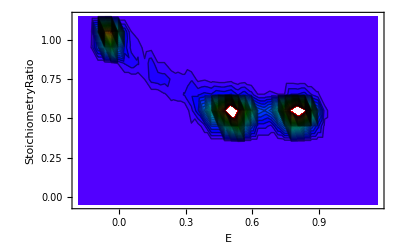

```mathematica
FSetPIEGamma[1.2]
FParamHisto2D["E","StoichiometryRatio",{-0.2,1.2,.03},{-0.1,1.2,0.1},PlotRange->{0,200},Contours->40,ColorFunction->(If[#≠0,Hue[(0.73-.73#)],Hue[0.72]]&)]
```

| Related Guides
▪Fretica